```mathematica
a = 0.1
boat = ImplicitRegion[a*(x+1)^3 < y && -a*(x-1)^3 < y ,{{x,-4,4},{y,0,2}}];
boatthreed = ImplicitRegion[z*(x+1)^3 < y && -z*(x-1)^3 < y ,{{x,-4,4},{y,0,2}, {z,0.1,2 }}];
Region[boat]
RegionPlot3D[(z^2*0.01)*(x+1)^3 < y && -(z^2*0.01)*(x-1)^3 < y, {x,-4,4},{y,0,2}, {z,0.1,4}, AxesLabel->{"x","y","z"}]
RegionPlot3D[(0.1)*(x+1)^3 < y && -(0.1)*(x-1)^3 < y, {x,-4,4},{y,0,2}, {z,-4,4}, AxesLabel->{"x","y","z"}]
RegionPlot3D[(z^2*0.1)*(x+1)^3 < y && -(z^2*0.1)*(x-1)^3 < y, {x,-4,4},{y,0,2}, {z,-4,4}, AxesLabel->{"x","y","z"}]
```

0.1

```mathematica
Manipulate[RegionPlot[a*(x+1)^3 < y && -a*(x-1)^3 < y ,{x,-4,4},{y,0,2}, PlotPoints->75],{a,0.01,2}]
```

```mathematica
slicer[zslice_, theta_]:=Module[{},
boat = ImplicitRegion[zslice*(x+1)^3 < y && -zslice*(x-1)^3 < y ,{{x,-4,4},{y,0,2}}];
water = ImplicitRegion[If[theta<90,y<Tan[theta Degree]*x+d,y>Tan[theta Degree]*x+d],{{x,-2,2},{y,-2,2}}];
(*Mass is equal to ballast of 700-1000g, mast is 98g, hardboard mass is *)
mass = 21000;
com = {0,1.25,0};
under = RegionIntersection[boat,water];
disp = 1000*10*Area[under];
draft = N[d/.FindRoot[disp==mass,{d,-20,20}][[1]]];
cob = Append[RegionCentroid[under/.{d->draft}],0];
buoyancy = mass*98/10*{-Sin[theta Degree],Cos[theta Degree],0};
torque = Cross[cob-com,buoyancy][[3]];
torque]
rmdata[slice_]:= Module[{},Parallelize[Table[{theta,slicer[0.1,theta]},{theta,{10,20,30,40,50,60,70,80,100,110,120,130,140,150,160,170,180}}]]]
```

```mathematica
dataset =Table[{slice,rmdata[slice]},{slice,{0.05, 0.1,0.3,0.4}}]
```

{{0.05,{{10,15324.7},{20,32896.3},{30,50116.1},{40,53814.1},{50,49677.7},{60,40985.},{70,29526.1},{80,16564.3},{100,-10264.},{110,-23490.5},{120,-35390.7},{130,-44684.5},{140,-49556.8},{150,-46692.7},{160,-30457.9},{170,-14091.},{180,-2.09133×10^-12}}},{0.1,{{10,15324.7},{20,32896.3},{30,50116.1},{40,53814.1},{50,49677.7},{60,40985.},{70,29526.1},{80,16564.3},{100,-10264.},{110,-23490.5},{120,-35390.7},{130,-44684.5},{140,-49556.8},{150,-46692.7},{160,-30457.9},{170,-14091.},{180,-2.09133×10^-12}}},{0.3,{{10,15324.7},{20,32896.3},{30,50116.1},{40,53814.1},{50,49677.7},{60,40985.},{70,29526.1},{80,16564.3},{100,-10264.},{110,-23490.5},{120,-35390.7},{130,-44684.5},{140,-49556.8},{150,-46692.7},{160,-30457.9},{170,-14091.},{180,-2.09133×10^-12}}},{0.4,{{10,15324.7},{20,32896.3},{30,50116.1},{40,53814.1},{50,49677.7},{60,40985.},{70,29526.1},{80,16564.3},{100,-10264.},{110,-23490.5},{120,-35390.7},{130,-44684.5},{140,-49556.8},{150,-46692.7},{160,-30457.9},{170,-14091.},{180,-2.09133×10^-12}}}}

```mathematica
(*dataset = Parallelize[Table[{theta,slicer[0.1,theta]},{theta,{10,20,30,40,50,60,70,80,100,110,120,130,140,150,160,170,180}}]];*)
```

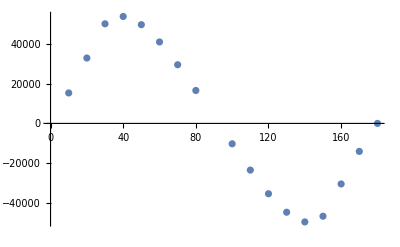

```mathematica
ListPlot[rmcurve[0.1]]
```